# Wolfram Language Basics

## Daily Study Group (Feb 15-Mar 5, 2021)

## Cloud Functions

### FormPage

```mathematica
mailBin=CreateDatabin[]
```

```mathematica
mailSender[email_,date_,subj_,body_]:=(CloudDeploy@ScheduledTask[
SendMail[<|"To"->email,"Subject"->subj,"Body"->body|>],
{date}];
DatabinAdd[mailBin,<|"Recipient"->email,"DateTime"->date,"Subject"->subj,"Body"->body|>];
"Mail queued for "<>DateString@date<>".\n\nSending to "<>email<>" with subject \""<>subj<>"\" and body \""<>body<>"\".")
```

```mathematica
CloudDeploy[FormFunction[{"email"-><|"Label"->"Email","Interpreter"->"EmailAddress","Hint"->"your email address"|>,
"date"-><|"Label"->"Date & Time","Interpreter"->"DateTime","Hint"->"date and time to send"|>,
"subj"-><|"Label"->"Subject","Interpreter"->"String","Hint"->"subject (if you want one)"|>->"",
"body"-> <|"Label"->"Body","Interpeter"->"String","Hint"->"email body"|>->""},
mailSender[#email,#date,#subj,#body]&],
"/MailTestStudyGroup"]
```

### APIFunction

```mathematica
CloudDeploy[
APIFunction[
"v" -> DelimitedSequence["Number"],
BarChart[#v,ColorFunction->"CandyColors"]&,
"PNG"
],"BarCharter"]
```

### Redeploy Cloud Objects

```mathematica
CloudDeploy[
APIFunction[
"v" -> DelimitedSequence["Number"],
BarChart[#v,ColorFunction->"CandyColors"]&,
"PNG"
],"BarCharter"]
```

## Audio/Video

Audio and video files can be found in the shared “data” folder.

### Join Video

```mathematica
vid1=Video["/data/hoffmann_ohno.mp4"]
vid2=Video["/data/n0ne sequence.mp4"]
```

Video[/Users/arbenk/Wolfram U Examples/hoffmann_ohno.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/arbenk/Wolfram U Examples/hoffmann_ohno.mp4Thumbnail1StandardForm

Video[/Users/arbenk/Wolfram U Examples/n0ne sequence.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/arbenk/Wolfram U Examples/n0ne sequence.mp4Thumbnail1StandardForm

```mathematica
VideoJoin[vid1,vid2]
```

Video[/Users/arbenk/Documents/Wolfram/Video/VideoJoin-91fc92d4-8351-45de-b83e-23e1a21b573e.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/arbenk/Documents/Wolfram/Video/VideoJoin-91fc92d4-8351-45de-b83e-23e1a21b573e.mp4Thumbnail1StandardForm

### Audio Equality

```mathematica
audio1=Import["data/ohno1.mp3",IncludeMetaInformation->None]
audio2=Import["data/ohno2.mp3",IncludeMetaInformation->None]
audio3=Import["data/ohno3.wav",IncludeMetaInformation->None]
```

```mathematica
audio1==audio2
```

False

### Drop Frame Mode

Should be able to do work with these things with VideoMap/VideoFrameMap...?

## Machine Learning

### Using the GPU

```mathematica
smallNumbers=RandomReal[{-5,5},1000];
```

```mathematica
bigNumbers=RandomReal[{5,15},1000];
```

```mathematica
numberSizer=Classify[<|"Small"->smallNumbers,"Big"->bigNumbers|>]
```

ClassifierFunction[…]

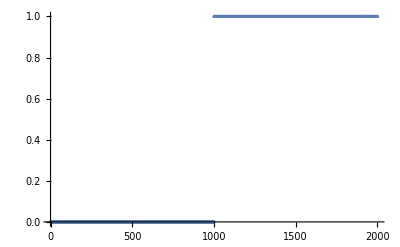

```mathematica
ListPlot[Table[numberSizer[x],{x,-5,15,.01}]/.{"Big"->1,"Small"->0}]
```

```mathematica
numberSizerGPU=Classify[<|"Small"->smallNumbers,"Big"->bigNumbers|>,TargetDevice->"GPU"]
```

Classify::trgdevmac: TargetDevice -> "GPU" is not supported on Mac OS platforms.

## Numerics & Symbolics

### Differential Equations

```mathematica
DSolve[{x'[t]+x[t]==a Sin[t]},x[t],t]
```

```mathematica
sol=DSolve[{x'[t]+x[t]==a Sin[t],x[0]==0},x[t],t]
```

```mathematica
x[t]/.sol
```

```mathematica
sol[[1,1,2]]
```

### WorkingPrecision & PrecisionGoal

```mathematica
Integrate[Sin[x]^2,{x,0,π}]
```

```mathematica
int=NIntegrate[Sin[x]^2,{x,0,π}]
```

```mathematica
N[int,20]
```

```mathematica
N[π/2,30]
```

```mathematica
π/2-int
```

```mathematica
intWorking15=NIntegrate[Sin[x]^2,{x,0,π},WorkingPrecision->15]
N[π/2,30]
```

```mathematica
intGoal15=NIntegrate[Sin[x]^2,{x,0,π},PrecisionGoal->15]
N[π/2,30]
```

### Solving Linear Systems

```mathematica
Solve[{3x+4y==3,-2x+8y==9},{x,y}]
```

```mathematica
LinearSolve[{{3,4},{-2,8}},{3,9}]
```

### NDSolve Example with Reap and Sow ?

```mathematica
soln=Reap[
NDSolve[{f''[x]+f'[x]+f[x]==0,f[0]==1,f'[0]==1},f,{x,0,10},EvaluationMonitor:>Sow[{x,f[x]}]]
];
```

```mathematica
NDSolve[{f''[x]+f'[x]+f[x]==0,f[0]==1,f'[0]==1},f,{x,0,10},EvaluationMonitor:>Print["x = ",x,", f[x] = ",f[x]]
]
```

```mathematica
xfPairs={}
```

```mathematica
NDSolve[{f''[x]+f'[x]+f[x]==0,f[0]==1,f'[0]==1},f,{x,0,10},EvaluationMonitor:>AppendTo[xfPairs,{x,f[x]}]
]
```

```mathematica
xfPairs==Last@Last@soln
```

### NIntegrate with Messy Functions

```mathematica
Integrate[Sin[Sin[x]],{x,0,2}]
```

```mathematica
NIntegrate[Sin[Sin[x]],{x,0,2}]
```

```mathematica
Integrate[Sin[Sin[x]/x]/x,{x,1,2}]
```

```mathematica
NIntegrate[Sin[Sin[x]/x]/x,{x,1,10}]
```

```mathematica
NIntegrate[Sin[Sin[x]/x]/x,{x,1,10},WorkingPrecision->20]
```

```mathematica
Plot[Sin[Sin[x]/x]/x,{x,1,10},PlotRange->All]
```

```mathematica
Integrate[Sin[Sin[x^Cos[x]]],{x,0,8}]
```

∫_0^8 Sin[Sin[x^Cos[x]]]ⅆx

```mathematica
NIntegrate[Sin[Sin[x^Cos[x]]],{x,0,8},WorkingPrecision->20]
```

2.5499633678420613338

```mathematica
Plot[Sin[Sin[x^Cos[x]]],{x,0,8}]
```

## Notebooks and Wolfram Language (Tips and Tricks)

### Abort/Quit

```mathematica
Pause[30]
```

$Aborted

Abort: Evaluation -> Abort Evaluation (⌘ .)
Quit: Evaluation -> Quit Kernel

```mathematica
Quit
```

### Useful shortcuts

Reuse Input from above

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
%
```

{1,2,3,4,5,6,7,8,9,10}

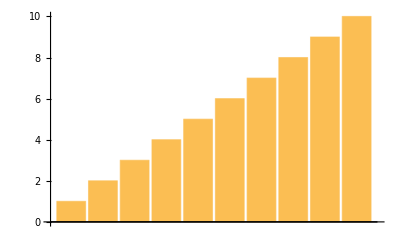

```mathematica
BarChart[%]
```

```mathematica
BarChart[%%%]
```

-Graphics-

Insert -> Input from Above (⌘ L or Ctrl L)
Insert -> Output from Above (⌘ Shift L or Ctrl Shift L)

```mathematica
In[1]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
In[-2]
```

{1,2,3,4,5,6,7,8,9,10}

["http://reference.wolfram.com/language/guide/WolframSystemSessionHistory.html"](http://reference.wolfram.com/language/guide/WolframSystemSessionHistory.html)

Style short cuts

Text
Section
Subsection
Input

Natural language input

=
Ctrl =

```mathematica
AirTemperatureData[Entity["City",{"Champaign","Illinois","UnitedStates"}]]
```

36. °F

```mathematica
LinguisticAssistant//FullForm
```

Entity["City",List["Paris","IleDeFrance","France"]]

Use Evaluate -> Evaluate in place to evaluate a piece of input in place without providing separate output cell:

Entity["City",List["Paris","IleDeFrance","France"]]

```mathematica
LinguisticAssistant
```

```mathematica
Entity["City",{"Champaign","Illinois","UnitedStates"}]
```

Delimiters

```mathematica
Grid[{
Style[#,Bold]&/@{"Keyboard Shortcut","Inserts","Menu Item"},
{ "Cmd Option ] or Alt ]", "[]","Insert ▶ Typesetting ▶ Matching []"},
{"Cmd Option } or Alt }", "{}","Insert ▶ Typesetting ▶ Matching {}"},
{"Cmd Option ) or Alt )", "()","Insert ▶ Typesetting ▶ Matching ()"}
},Alignment->Left,Spacings->{2,Automatic}]
```

Keyboard Shortcut | Inserts | Menu Item
Cmd Option ] or Alt ] | [] | Insert ▶ Typesetting ▶ Matching []
Cmd Option } or Alt } | {} | Insert ▶ Typesetting ▶ Matching {}
Cmd Option ) or Alt ) | () | Insert ▶ Typesetting ▶ Matching ()

### Rules

Association

```mathematica
test =<|a-> 1,b-> 2,c-> 3|>
```

<|a→1,b→2,c→3|>

```mathematica
test[a]
```

1

```mathematica
test[[Key[a]]]
```

1

```mathematica
AssociationThread[CharacterRange["a","f"],Range[6]]
```

<|a→1,b→2,c→3,d→4,e→5,f→6|>

```mathematica
MapThread[Rule,{CharacterRange["a","f"],Range[6]}]
```

{a→1,b→2,c→3,d→4,e→5,f→6}

ReplaceAll

```mathematica
Thread[CharacterRange["a","z"]->ToString/@ Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
StringReplace["Hello",%,IgnoreCase->True]
```

85121215

### Stylesheets

["http://reference.wolfram.com/language/guide/Stylesheets.html"](http://reference.wolfram.com/language/guide/Stylesheets.html)

["http://reference.wolfram.com/language/tutorial/WorkingWithStylesheets.html"](http://reference.wolfram.com/language/tutorial/WorkingWithStylesheets.html)

### Making file non-saveable

```mathematica
SetOptions[EvaluationNotebook[],Saveable-> False]
```

### Nonstandard Evaluation (Hold*)

["http://reference.wolfram.com/language/tutorial/EvaluationOfExpressions.html"](http://reference.wolfram.com/language/tutorial/EvaluationOfExpressions.html)

### Error Handling

["http://reference.wolfram.com/language/guide/RobustnessAndErrorHandling.html"](http://reference.wolfram.com/language/guide/RobustnessAndErrorHandling.html)

Runtime: Confirm, Enclose

Low Level: Check, Throw Catch

Messages: https://reference.wolfram.com/language/tutorial/TextualInputAndOutput.html#12413

### Debugging

["http://reference.wolfram.com/language/workflowguide/ErrorsAndDebugging.html"](http://reference.wolfram.com/language/workflowguide/ErrorsAndDebugging.html)

### Package editor

https://support.wolfram.com/27221

File -> New -> Package/Script -> Wolfram language Package

## Resources for Broader Topics

New in 12.2:

https://writings.stephenwolfram.com/2020/12/launching-version-12-2-of-wolfram-language-mathematica-228-new-functions-and-much-more/

https://reference.wolfram.com/language/guide/SummaryOfNewFeaturesIn122.html

Visualization using WL

https://www.wolfram.com/wolfram-u/catalog/visualization-graphics/

https://reference.wolfram.com/language/guide/DataVisualization.html

https://reference.wolfram.com/language/guide/ChartingAndInformationVisualization.html

Machine Learning

https://www.wolfram.com/wolfram-u/catalog/machine-learning/

https://www.wolfram.com/wolfram-u/machine-learning-basics/

https://www.wolfram.com/wolfram-u/machine-learning-zero-to-AI-60-minutes/

https://www.wolfram.com/wolfram-u/multiparadigm-data-science/classification.html

Image processing

https://www.wolfram.com/wolfram-u/introduction-to-image-processing/

Audio and speech processing

https://www.wolfram.com/wolfram-u/neural-networks-applications-audio-processing/

Video importing and exporting

https://reference.wolfram.com/language/tutorial/VideoBasics.html

https://reference.wolfram.com/language/tutorial/ImportingAndExportingVideo.html

Solving differential equations

https://reference.wolfram.com/language/tutorial/DSolveOverview.html

https://reference.wolfram.com/language/tutorial/NumericalOperationsOnFunctions.html#17230

Workbench

https://www.wolfram.com/workbench/

https://reference.wolfram.com/workbench/index.jsp

https://www.wolfram.com/broadcast/c?c=93

Linear programming

https://reference.wolfram.com/language/tutorial/ConstrainedOptimizationLinearProgramming.html

Working with large arrays

https://reference.wolfram.com/language/tutorial/SymbolicTensors.html

Approximating data

https://reference.wolfram.com/language/tutorial/Numbers.html#21155

Statistical Analysis of Experimental Data

Functionailty:

https://reference.wolfram.com/language/guide/StatisticalModelAnalysis.html

https://reference.wolfram.com/language/guide/CurveFittingAndApproximateFunctions.html

https://reference.wolfram.com/language/tutorial/NumericalOperationsOnData.html#382930361

## Overall Review

### Day 1: Get Started with the Wolfram Language

### Day 2: Beginning Programming

### Day 3: Graphics and Visualizations

### Day 4: Symbolics

### Day 5: Numerics

### Day 6: Advanced Programming

### Day 7: Working with Data

### Day 8: Machine Learning

### Day 9: Images, Video and Audio

### Day 10: Using Notebooks Effectively

### Day 11: Tips and Tricks

### Day 12: Cloud Functions